```mathematica
ClearAll["Global`*"]
```

```mathematica
temp1=ListCorrelate[{1,1,1,1},{0,0,0,1,1,1,1,0,0,0}]
StandardDeviation[temp1]//N
```

{1,2,3,4,3,2,1}

1.1127

```mathematica
temp2=ListCorrelate[{1,1,0,1},{0,0,0,1,1,1,1,0,0,0}]
StandardDeviation[temp2]//N
```

{1,1,2,3,2,2,1}

0.755929

```mathematica
temp3=ListCorrelate[{1,1,2,1},{0,0,0,1,1,1,1,0,0,0}]
StandardDeviation[temp3]//N
```

{1,3,4,5,4,2,1}

1.57359

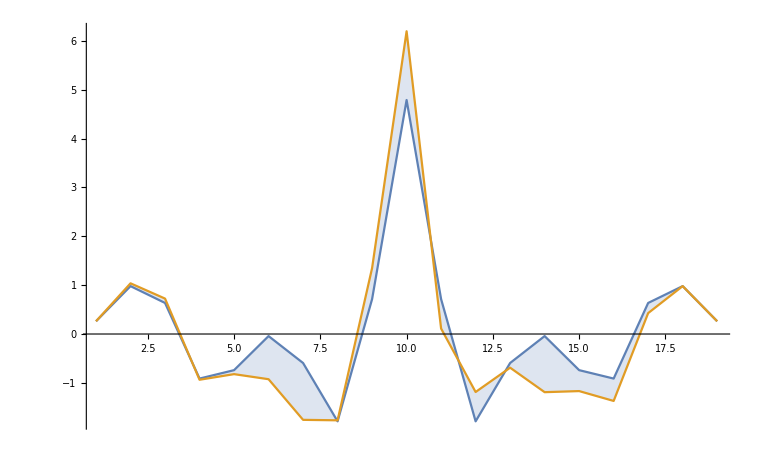

```mathematica
len=10;
temp4=RandomReal[{-1,1},len];
pad4=Prepend[Append[temp4,ConstantArray[0,len-1]],ConstantArray[0,len-1]]//Flatten;
ker4=ReplacePart[temp4,{3->temp4[[3]]*2.9,9->temp4[[9]]*1.1,5->temp4[[5]]*2.4}];
acor4=ListCorrelate[temp4,pad4];
cor4=ListCorrelate[ker4,pad4];
ListPlot[{acor4,cor4},Joined->True,PlotRange->All,ImageSize->Large,Filling->{1->{2}}]
```